```mathematica
<<Utilities`CleanSlate`
ClearAll["Global`*"]
LHS = Assuming[{c>R>0},∫_R^c p A ⅇ^(-(B p r)/(Eo δ c))ⅆr];
LHS = Normal[Series[%,{R,0,1}]];
RHS = Log[Q];
Sol1 =  Solve[LHS==RHS,c];
c = Normal[c/.Sol1[[1]]];
Ec[R_] = δ Eo c/R;
Vc[R_] = δ Eo c Log[R2/R];
Sol2 = Flatten[Solve[D[Vc[R], R]==0,R]];
Vmin = Simplify[Vc[R]/.Sol2];
Rmin = R/.Sol2;
(*Rmin =Simplify[Normal[Series[Rmin,{R2,∞,1}]]];*)
Print["Ec[R] = ",Ec[R], " (V/m)"];
Print["Vc[R] = ",Vc[R], " (V)"];
Print["Rmin = ",Rmin, " (m)"];
Print["Vmin = ",Vmin, " (V)"];
```

{{c→(B ⅇ^((B p)/(Eo δ)) (A p R+Log[Q]))/(A (-1+ⅇ^((B p)/(Eo δ))) Eo δ)}}

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Vc[R] = (B ⅇ^((B p)/(Eo δ)) (A p R+Log[Q]) Log[R2/R])/(A (-1+ⅇ^((B p)/(Eo δ)))) (V)

Rmin = -Log[Q]/(A p ProductLog[-(ⅇ Log[Q])/(A p R2)]) (m)

Vmin = (B ⅇ^((B p)/(Eo δ)) Log[-(A p R2 ProductLog[-(ⅇ Log[Q])/(A p R2)])/Log[Q]] (Log[Q]-Log[Q]/ProductLog[-(ⅇ Log[Q])/(A p R2)]))/(A (-1+ⅇ^((B p)/(Eo δ)))) (V)

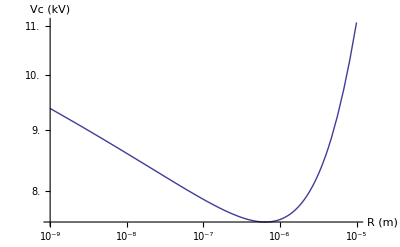

```mathematica
A = 7;
B = 258;
Q = 10^4;
p= 101325;
δ = 1;
Eo = 31 10^5;
R2 = 1000;
LogLogPlot[Vc[R]/1000, {R,10^-9,10^-5}, AxesLabel-> {"R (m)", "Vc (kV)"}]
```